```mathematica
θ=π/8
```

π/8

```mathematica
R=3
r=1
```

3

1

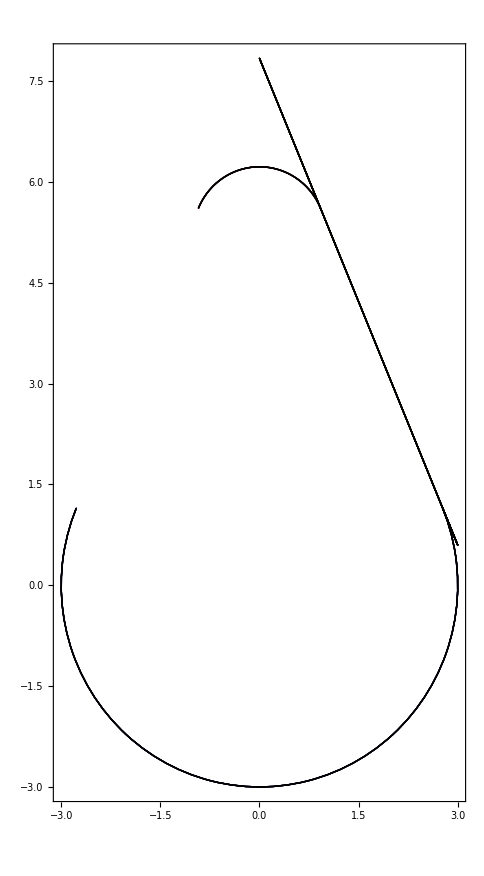

```mathematica
x[t_]:=R Cos[t]
y[t_]:=R Sin[t]
x1[t_]:=r Cos[t]
y1[t_]:=r Sin[t]+(R-r)/Sin[θ]
ParametricPlot[{{x[t],y[t]},{x1[u],y1[u]},{Abs[x[t]],R*Sin[θ]-1./Tan[θ]*Abs[x[t]]+R*Cos[θ]^2/Sin[θ]}},{t,π-θ,2π+θ},{u,θ,π-θ}]
```

```mathematica
y'[θ]/x'[θ]
```

-Cot[π/8]

```mathematica
R=.
r=.
θ=.
```

```mathematica
Sqrt[(x1[θ]-x[θ])^2+(y1[θ]-y[θ])^2]
```

√((r Cos[θ]-R Cos[θ])^2+((-r+R) Csc[θ]+r Sin[θ]-R Sin[θ])^2)

```mathematica
FullSimplify[√((r Cos[θ]-R Cos[θ])^2+((-r+R) Csc[θ]+r Sin[θ]-R Sin[θ])^2)]
```

√((r-R)^2 Cot[θ]^2)

```mathematica
La condiione affichè i lati della goccia siano < lunghezza di persistenza è 
L=Sqrt[0.1*0.06]
Solve[Tan[θ]==1/Sqrt[L],θ]
```

affichè condiione della goccia i La lati siano<di è lunghezza persistenza

0.0774597

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ→1.29935}}

```mathematica
"Lunghezza del segmento tangente"
L=Simplify[Sqrt[(R*Cos[θ]-r*Cos[θ])^2+((R-r)/Sin[θ]+r*Sin[θ]-R*Sin[θ])^2]] 
"Perimetro"
FullSimplify[2*L+r*(pi-2*θ)+R*(π+2*θ),Assumptions->R-r>0&&r>0&&0<θ<π/2]
"Area"
Simplify[R^2/2*(π+2*θ)+r^2/2*(π-2*θ)+2*(R+r)*L/2,Assumptions->R-r>0&&r>0&&0<θ<π/2]
```

Lunghezza del segmento tangente

√((r-R)^2 Cot[θ]^2)

Perimetro

pi r+π R-2 r θ+2 R θ+2 (-r+R) Cot[θ]

Area

1/2 (π (r^2+R^2)+2 (-r^2+R^2) θ-2 (r^2-R^2) Cot[θ])

```mathematica
R=1.
r=0.02
θ=π/12
```

1.

0.02

π/12